```mathematica
Remove["Global`*"]
```

```mathematica
h = {{0,ϵ*/2,0},{ϵ/2,δ,Sqrt[2]ϵ*/2},{0,Sqrt[2]ϵ/2,α+2δ}}
```

{{0,Conjugate[ϵ]/2,0},{ϵ/2,δ,Conjugate[ϵ]/(√2)},{0,ϵ/(√2),α+2 δ}}

```mathematica
h // MatrixForm
```

(0 | Conjugate[ϵ]/2 | 0
ϵ/2 | δ | Conjugate[ϵ]/(√2)
0 | ϵ/(√2) | α+2 δ)

```mathematica
CharacteristicPolynomial[h /.{α->0,δ->0},λ]
```

-λ^3+3/4 ϵ λ Conjugate[ϵ]

```mathematica
Eigenvectors[Assuming[ϵ>0,FullSimplify[h]] //.{α->0,δ->-Sqrt[3.]/2.ϵ,ϵ->1}]
```

{{0.118621,-0.511825,0.850861},{0.494978,-0.712368,-0.497523},{0.86077,0.480174,0.168841}}

```mathematica
evs=Map[#/Norm[#]&,Assuming[ϵ>0,FullSimplify[Eigenvectors[h //.{α->0,δ->-γ*ϵ,ϵ->1}]]]];
```

```mathematica
NMaximize[Abs[evs[[1]][[1]]*evs[[1]][[2]]]+Abs[evs[[2]][[1]]*evs[[2]][[2]]]+Abs[evs[[3]][[1]]*evs[[3]][[2]]] ,{γ}]
```

{0.898854,{γ→-0.553521}}

```mathematica
values = Map[{#/Sqrt[3],Abs[evs[[1]][[1]]*evs[[1]][[2]]]+Abs[evs[[2]][[1]]*evs[[2]][[2]]]+Abs[evs[[3]][[1]]*evs[[3]][[2]]] /.{γ->#}}&,-Sqrt[3]*Range[0.3,0.4,0.001]];
```

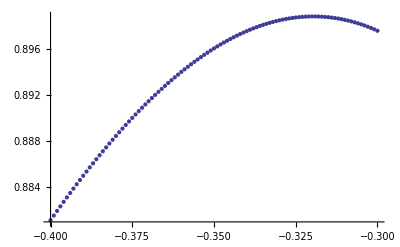

```mathematica
ListPlot[values]
```

```mathematica
Clear[gaussianPulse]
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0-4*dt]<w && t≥t0+4*dt:=w/(w+Sqrt[2π ]dt)
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0-4*dt]≥w&& t > t0+4*dt:=Exp[-(t-t0-w-4*dt)^2/dt^2/2]*w/(w+Sqrt[2π ]dt)
gaussianPulse[t_,t0_,w_,dt_]/;  t <= t0+4*dt:=Exp[-(t-t0-4*dt)^2/dt^2/2]*w/(w+Sqrt[2π ]dt)
```

```mathematica
heff = h /. {δ->0.,α->-.240,ϵ->π 0.1 *gaussianPulse[t,10,20,5]};
psisolution = NDSolve[{psi'[t] == -I heff. psi[t],psi[0]=={1,0,0}},psi,{t,0,100}];
```

```mathematica
drive[ϕ_,t_]:= π 0.1 *(gaussianPulse[t,3,5.,1.]+Exp[I ϕ] *gaussianPulse[t,15,5.,1.])
hϕ[t_,ϕ_]:= Block[{δ=-0.16,α=-.240*2,ϵ=drive[ϕ,t]},h /. {δ->δ,α->α,ϵ->ϵ,ϕ->ϕ}] ;
phisolution[ϕ_] := NDSolve[{psi'[t] == -I hϕ[t,ϕ]. psi[t],psi[0]=={1,0,0}},psi,{t,0,30}];
phisequence[ϕ_]:=1-Evaluate[Abs[psi[30.0] /. phisolution[ϕ] ] [[1]]][[1]]^2;
```

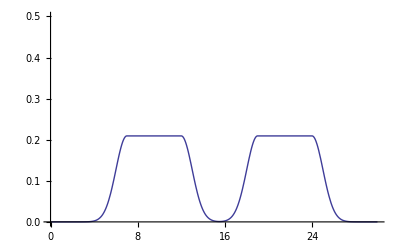

```mathematica
Plot[drive[0,t],{t,0,30},PlotRange->{0,0.5}]
```

```mathematica
phases =Range[0,4π,π/8];
values = Map[phisequence[#]&,phases];
```

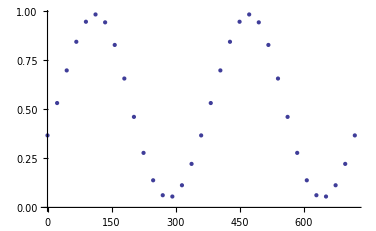

```mathematica
ListPlot[Map[{phases[[#]]*180./π,values[[#]]}&,Range[1,Length[phases]]]]
```

```mathematica
Remove["hrabi"]
hrabi[δ_,α_,ϵ_] := h  /.{δ->δ,α->α,ϵ->ϵ};
hrabi[δ,α,ϵ] //MatrixForm
Remove["rabisolution"]
rabisolution[δ_,α_,ϵ_] := Evaluate[NDSolve[{psi'[t] == -I hrabi[δ,α,ϵ]. psi[t],psi[0]=={1,0,0}},psi,{t,0,100}] /. {δ->δ,α->α,ϵ->ϵ} ]
```

Remove::rmnsm: There are no symbols matching ""hrabi"".

(0 | Conjugate[ϵ]/2 | 0
ϵ/2 | δ | Conjugate[ϵ]/(√2)
0 | ϵ/(√2) | α+2 δ)

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

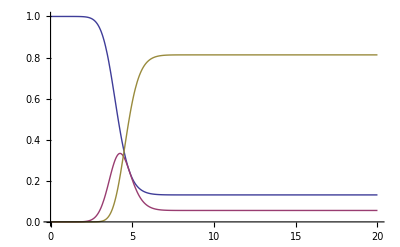

```mathematica
d = 0.1;
ep = 0.2;
myrabisolution = rabisolution[δ,α,ϵ] /. {δ->-0.35*0,α->-0.240 2 π*0,ϵ->1./d*π  *gaussianPulse[t,0,d,1.0]};
psit =(Abs[Evaluate[psi[t] /. myrabisolution]])[[1]];
Plot[{psit[[1]]^2,psit[[2]]^2,psit[[3]]^2},{t,0,20},PlotRange->{0,1}]
```

```mathematica
Remove["rabistate"]
rabistate[δ_?NumberQ,α_?NumberQ,ϵ_?NumberQ,t_] := Evaluate[psi[t] /. rabisolution[δ,α,ϵ]][[1]]
rabisolution[0.1,-0.24,0]
```

Remove::rmnsm: There are no symbols matching ""rabistate"".

{{psi→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
values = Map[Abs[rabistate[0,-0.24,0.1,#]][[1]]&,Range[0,100]];
```

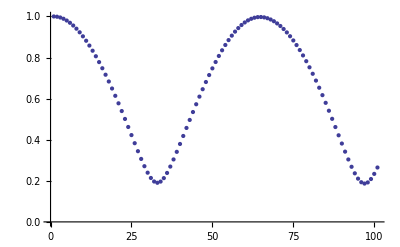

```mathematica
ListPlot[values]
```

```mathematica
deltas = Range[-0.25,0.25,0.01];
ts = Range[0,100];
values = Map[Block[{δ=#},Map[Abs[rabistate[δ 2 π,-0.24 2 π,0.2π,#]]&,ts]]&,deltas];
```

$Aborted

```mathematica
valuesi[j_]:=Map[Block[{i=#},Map[values[[i]][[#]][[j]]&,Range[1,Length[values[[1]]]]]]&,Range[1,Length[values]]];
```

```mathematica
valueslist = Map[valuesi[#]&,Range[1,3]];
```

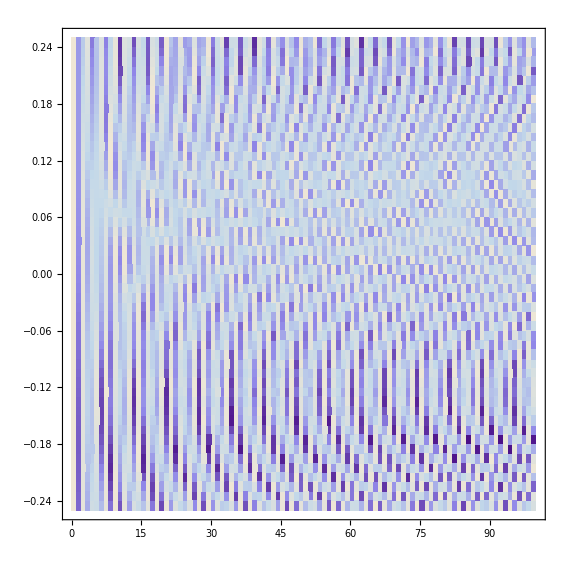
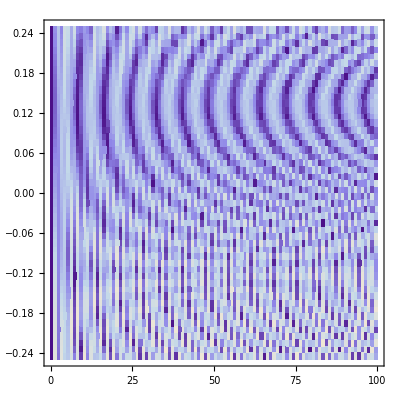
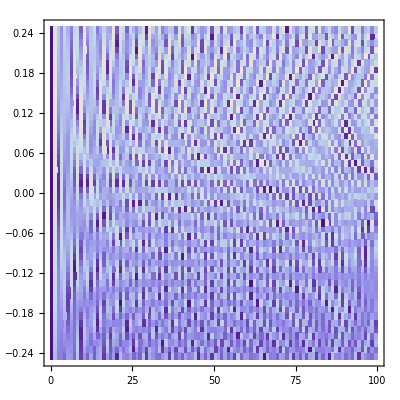

```mathematica
Map[ListDensityPlot[#,DataRange->{{ts[[1]],ts[[-1]]},{deltas[[1]],deltas[[-1]]}},InterpolationOrder->0,PlotRange->{0,1.1}]&,valueslist]
```

```mathematica
hreal = ComplexExpand[h ]  /.{α->1.}
```

{{0,ϵ/2,0},{ϵ/2,δ,ϵ/(√2)},{0,ϵ/(√2),1.+2 δ}}

```mathematica
hevs = Eigenvalues[hreal]
hevecs = Eigenvectors[hreal]
```

{Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,1],Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,2],Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,3]}

{{-(0.707107+1.41421 δ-0.707107 Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,1])/Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,1],-(1.41421 (1.+2. δ-1. Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,1]))/ϵ,1.},{-(0.707107+1.41421 δ-0.707107 Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,2])/Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,2],-(1.41421 (1.+2. δ-1. Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,2]))/ϵ,1.},{-(0.707107+1.41421 δ-0.707107 Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,3])/Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,3],-(1.41421 (1.+2. δ-1. Root[0.25 ϵ^2+0.5 δ ϵ^2+(1. δ+2. δ^2-0.75 ϵ^2) #1+(-1.-3. δ) #1^2+1. #1^3&,3]))/ϵ,1.}}

```mathematica
wp = {δ->δ,ϵ->ϵ};
hevecswp = hevecs /. wp;
hevecswp = Map[#/Norm[#]&,hevecswp];
hevswp = hevs /. wp;
```

```mathematica
osc= Total[Map[hevecswp[[#]]*hevecswp[[#]][[1]]*Exp[-I hevswp[[#]]t]&,Range[1,Length[hevswp]]]];
```

```mathematica
osc /.{δ->0,t->1,ϵ->1}
```

{0.882455-0.000981418 ⅈ,0.00958007-0.441741 ⅈ,-0.152568+0.0526078 ⅈ}

```mathematica
Maximize[{Abs[osc[[2]] /. {ϵ->1}]^2,δ<0,t>0},{t,δ}]
```

{0.580679,{t→4.12527,δ→0.}}

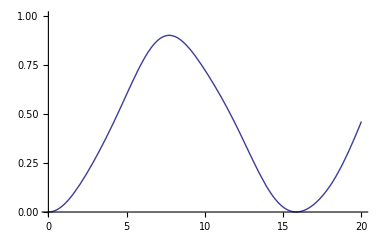

```mathematica
Plot[Abs[osc[[2]]/.{ϵ->0.4,δ->-0.01}]^2 ,{t,0,20},PlotRange->{0,1}]
```

```mathematica
epsilons = Range[0.1,2.0,0.1];
errorsvsϵ = Map[{#,Maximize[{Abs[osc[[2]] /.{ϵ->#}],δ<0,t>0},{t,δ}][[1]]}&,epsilons];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Export[NotebookDirectory[]<>"drive_errors_vs_epsilon.csv",Map[{#[[1]]/π,1-#[[2]]}&,errorsvsϵ],"CSV"]
```

E:\cygwin\home\adewes\thesis\material\mathematica\drive_errors_vs_epsilon.csv

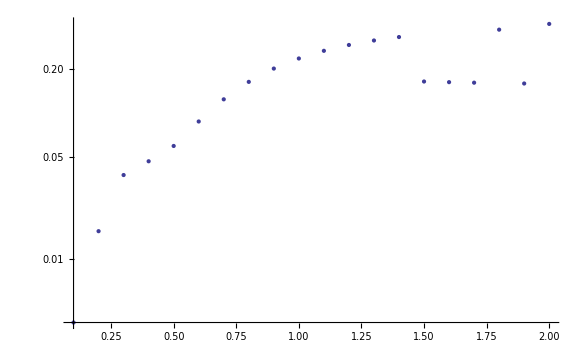

```mathematica
ListLogPlot[Map[{#[[1]],1-#[[2]]}&,errorsvsϵ],PlotRange->Full]
```

```mathematica
epsilons = Range[0.01,2.0,0.01];
errors = Map[Maximize[{Abs[osc[[2]] /.{ϵ->#}],δ>0,t>0},{t,δ}]&,epsilons];
```

```mathematica
gateerrors = Map[{epsilons[[#]],errors[[#]][[1]]}&,Range[1,Length[epsilons]]];
gatetimes = Map[{epsilons[[#]],errors[[#]][[2]][[1]][[2]]}&,Range[1,Length[epsilons]]];
detunings = Map[{epsilons[[#]],errors[[#]][[2]][[2]][[2]]}&,Range[1,Length[epsilons]]];
```

```mathematica
exportdata = Map[{gateerrors[[#]][[1]],gateerrors[[#]][[2]],gatetimes[[#]][[2]],detunings[[#]][[2]]}&,Range[1,Length[gateerrors]]];
```

```mathematica
Export[NotebookDirectory[]<>"drive_errors.csv",exportdata]
```

E:\cygwin\home\adewes\thesis\material\mathematica\drive_errors.csv

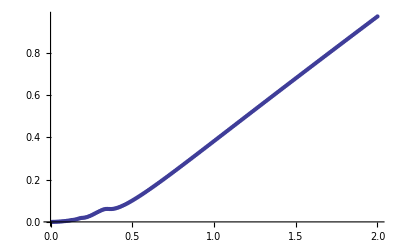

```mathematica
Show[ListPlot[detunings]]
```

```mathematica
Fit[detunings,{1,t},t]
```

-0.122728+0.529989 t

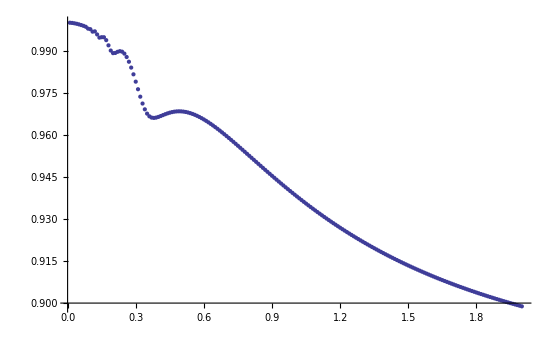

```mathematica
ListPlot[gateerrors,PlotRange->Full]
```

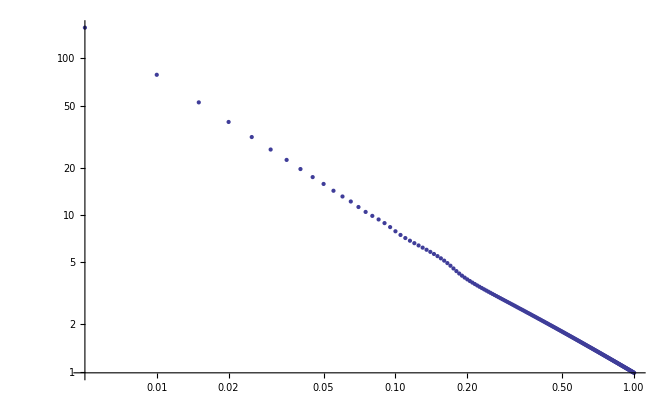

```mathematica
ListLogLogPlot[gatetimes/2,PlotRange->Full]
```

```mathematica
DensityPlot[,{t,0,50},{δ,-0.5 ,0.5},WorkingPrecision->10,PlotPoints->80]
```

$Aborted

```mathematica
gridPoints = Map[Block[{t=#},Map[Block[{δ=#},Abs[osc[[2]] /. {ϵ->0.2π,δ->2π δ}]^2]&,Range[-2.0,2.0,0.025]]]&,Range[0,50,0.25]];
```

```mathematica
ListDensityPlot[gridPoints,InterpolationOrder->1,DataRange->{{-2/2/π,2/2/π},{0,50}}]
```

-Graphics-

```mathematica
Export["E:\\cygwin\\home\\adewes\\thesis\\material\\mathematica\\3_level_driving.xls",gridPoints,"XLS"]
```

E:\cygwin\home\adewes\thesis\material\mathematica\3_level_driving.xls